(5 √(2/π) Sin[4 w])/w

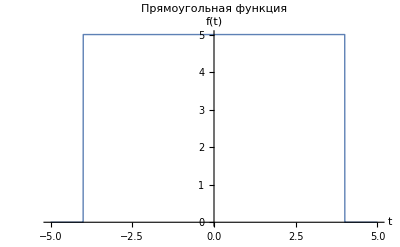

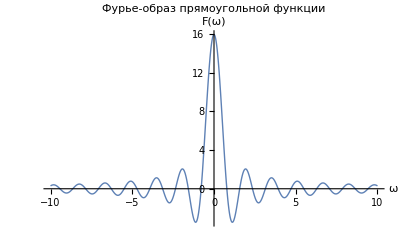

Проверка равенства Парсеваля:

∫|f(t)|.b2 dt = 200

∫|F(ω)|.b2 dω = 200

Результат: True

```mathematica
f[t_,a_,b_]:=Piecewise[{{a,Abs[t]<=b},{0,Abs[t]>b}}]

a=5;
b=4;
fourier=FourierTransform[f[t,a,b],t,w]

Plot[f[t,a,b],{t,-5,5},PlotRange->All,PlotStyle->Thick,AxesLabel->{"t","f(t)"},PlotLabel->"Прямоугольная функция",Exclusions->None]

Plot[Re[fourier],{w,-10,10},PlotRange->All,PlotStyle->Thick,AxesLabel->{"ω","F(ω)"},PlotLabel->"Фурье-образ прямоугольной функции"]

energyTimeDomain = Integrate[Abs[f[t, a, b]]^2, {t, -Infinity, Infinity}];

energyFrequencyDomain = Integrate[Abs[fourier]^2, {w, -Infinity, Infinity}];

Print["\nПроверка равенства Парсеваля:"]
Print["∫|f(t)|.b2 dt = ", energyTimeDomain]
Print["∫|F(ω)|.b2 dω = ", energyFrequencyDomain]
Print["Результат: ", energyTimeDomain == energyFrequencyDomain]
```

-(5 ⅇ^(-4 ⅈ w) (-1+ⅇ^(4 ⅈ w))^2)/(4 √(2 π) w^2)

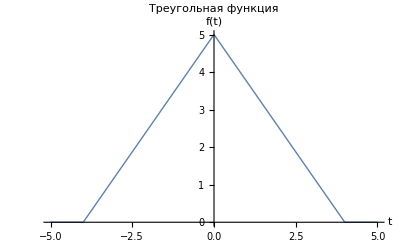

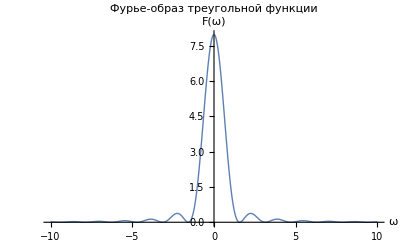

Проверка равенства Парсеваля:

∫|f(t)|.b2 dt = 200/3

∫|F(ω)|.b2 dω = 200/3

Результат: True

```mathematica
f[t_,a_,b_]:=Piecewise[{{a-Abs[a t/b],Abs[t]≤b},{0,Abs[t]>b}}]

a=5;
b=4;

fourier=FourierTransform[f[t,a,b],t,w]

Plot[f[t,a,b],{t,-5,5},PlotRange->All,PlotStyle->Thick,AxesLabel->{"t","f(t)"},PlotLabel->"Треугольная функция"]

Plot[Re[fourier],{w,-10,10},PlotRange->All,PlotStyle->Thick,AxesLabel->{"ω","F(ω)"},PlotLabel->"Фурье-образ треугольной функции"]

energyTimeDomain = Integrate[Abs[f[t, a, b]]^2, {t, -Infinity, Infinity}];

energyFrequencyDomain = Integrate[Abs[fourier]^2, {w, -Infinity, Infinity}];

Print["\nПроверка равенства Парсеваля:"]
Print["∫|f(t)|.b2 dt = ", energyTimeDomain]
Print["∫|F(ω)|.b2 dω = ", energyFrequencyDomain]
Print["Результат: ", energyTimeDomain == energyFrequencyDomain]
```

5/8 √(π/2) (Sign[4-w]+Sign[4+w])

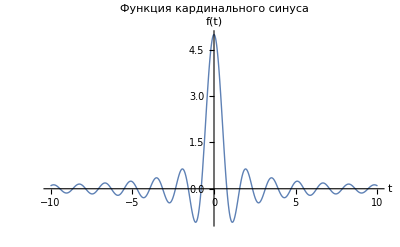

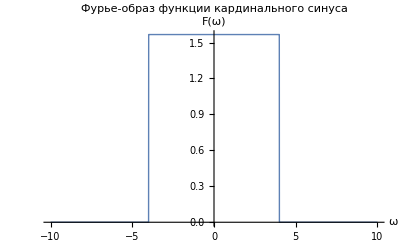

(25 π)/4

(25 π)/4

Проверка равенства Парсеваля:

∫|f(t)|.b2 dt = (25 π)/4

∫|F(ω)|.b2 dω = (25 π)/4

Результат: True

```mathematica
f[t_,a_,b_]:=a Sinc[b t]

a=5;
b=4;

fourier=FourierTransform[f[t,a,b],t,w]

Plot[f[t,a,b],{t,-10,10},PlotRange->All,PlotStyle->Thick,AxesLabel->{"t","f(t)"},PlotLabel->"Функция кардинального синуса"]

Plot[Re[fourier],{w,-10,10},PlotRange->All,PlotStyle->Thick,AxesLabel->{"ω","F(ω)"},PlotLabel->"Фурье-образ функции кардинального синуса", Exclusions->None]

energyTimeDomain=Integrate[Abs[f[t,a,b]]^2,{t,-Infinity,Infinity}]

energyFrequencyDomain=Integrate[Abs[fourier]^2,{w,-Infinity,Infinity}]

Print["\nПроверка равенства Парсеваля:"]
Print["∫|f(t)|.b2 dt = ", energyTimeDomain]
Print["∫|F(ω)|.b2 dω = ", energyFrequencyDomain]
Print["Результат: ", energyTimeDomain == energyFrequencyDomain]
```

√2 ⅇ^(-w^2/4)

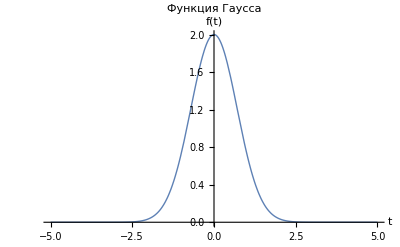

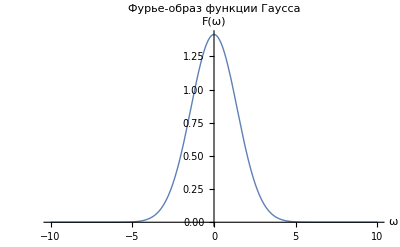

2 √(2 π)

2 √(2 π)

True

```mathematica
f[t_,a_,b_]:=a Exp[-b t^2]

a=2;
b=1;

fourier=FourierTransform[f[t,a,b],t,w]

Plot[f[t,a,b],{t,-5,5},PlotRange->All,PlotStyle->Thick,AxesLabel->{"t","f(t)"},PlotLabel->"Функция Гаусса"]

Plot[Re[fourier],{w,-10,10},PlotRange->All,PlotStyle->Thick,AxesLabel->{"ω","F(ω)"},PlotLabel->"Фурье-образ функции Гаусса"]

energyTimeDomain=Integrate[Abs[f[t,a,b]]^2,{t,-Infinity,Infinity}]

energyFrequencyDomain=Integrate[Abs[fourier]^2,{w,-Infinity,Infinity}]

Print["\nПроверка равенства Парсеваля:"]
Print["∫|f(t)|.b2 dt = ", energyTimeDomain]
Print["∫|F(ω)|.b2 dω = ", energyFrequencyDomain]
Print["Результат: ", energyTimeDomain == energyFrequencyDomain]
```

(2 √(2/π))/(4+w^2)

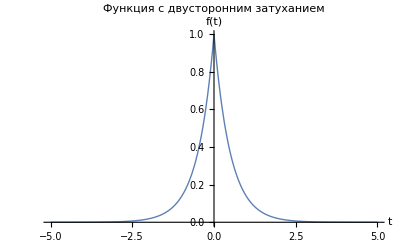

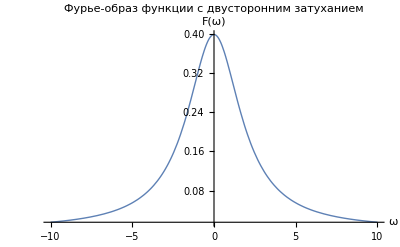

1/2

1/2

True

```mathematica
f[t_,a_,b_]:=a Exp[-b Abs[t]]

a=1;
b=2;

fourier=FourierTransform[f[t,a,b],t,w]

Plot[f[t,a,b],{t,-5,5},PlotRange->All,PlotStyle->Thick,AxesLabel->{"t","f(t)"},PlotLabel->"Функция с двусторонним затуханием"]

Plot[Re[fourier],{w,-10,10},PlotRange->All,PlotStyle->Thick,AxesLabel->{"ω","F(ω)"},PlotLabel->"Фурье-образ функции с двусторонним затуханием"]

energyTimeDomain=Integrate[Abs[f[t,a,b]]^2,{t,-Infinity,Infinity}]

energyFrequencyDomain=Integrate[Abs[fourier]^2,{w,-Infinity,Infinity}]

Print["\nПроверка равенства Парсеваля:"]
Print["∫|f(t)|.b2 dt = ", energyTimeDomain]
Print["∫|F(ω)|.b2 dω = ", energyFrequencyDomain]
Print["Результат: ", energyTimeDomain == energyFrequencyDomain]
```

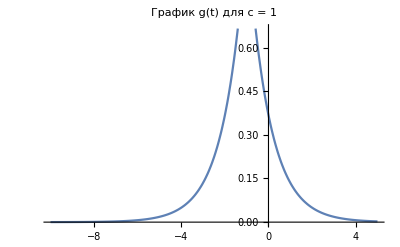
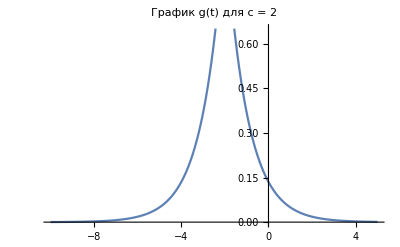
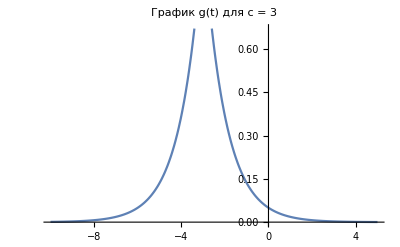

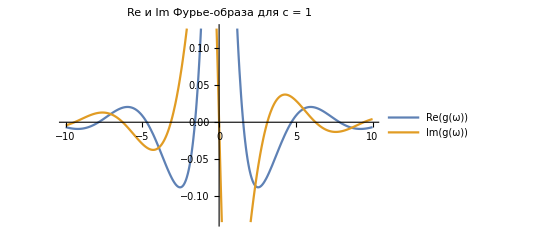
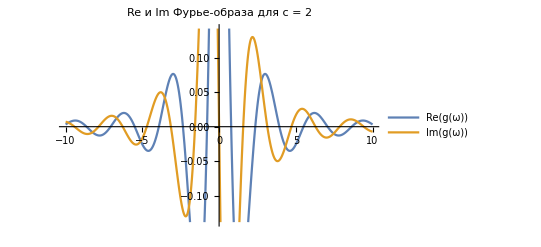
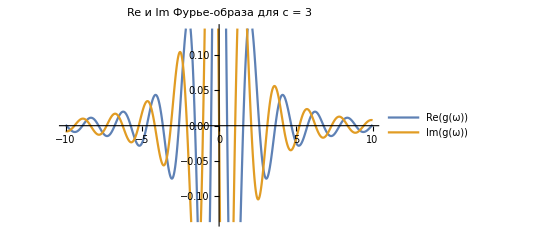

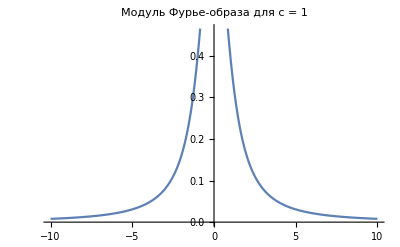
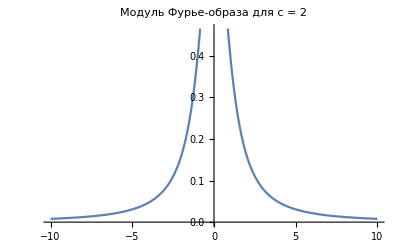

```mathematica
a=1;
b=1;
f[t_]:=a Exp[-b Abs[t]];

cValues={1,2,3};
g[t_,c_]:=f[t+c];

fourierTransforms=Table[FourierTransform[g[t,c],t,ω],{c,cValues}];

plotsG=Table[Plot[g[t,c],{t,-10,5},PlotLabel->"График g(t) для c = "<>ToString[c]],{c,cValues}]

plotsReIm=Table[Plot[{Re[fourierTransforms[[c]]],Im[fourierTransforms[[c]]]},{ω,-10,10},PlotLegends->{"Re(g(ω))","Im(g(ω))"},PlotLabel->"Re и Im Фурье-образа для c = "<>ToString[cValues[[c]]]],{c,Length[cValues]}]

plotsAbs=Table[Plot[Abs[fourierTransforms[[c]]],{ω,-10,10},PlotLabel->"Модуль Фурье-образа для c = "<>ToString[cValues[[c]]]],{c,Length[cValues]}]
```

```mathematica
ListLinePlot[Transpose[{⟦1,2⟧,⟦1,1⟧}],PlotLabel->"График fx(t)"]
```

NIntegrate::ilim: Invalid integration variable or limit(s) in {k,Length[t]}.

General::stop: Further output of NIntegrate::ilim will be suppressed during this calculation.

Part::pkspec1: The expression n cannot be used as a part specification.

Part::pkspec1: The expression k cannot be used as a part specification.

Part::pkspec1: The expression n cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

NIntegrate::ilim: Invalid integration variable or limit(s) in {k,Length[t]}.

NIntegrate::ilim: Invalid integration variable or limit(s) in {k, Length[t]}.

NIntegrate::ilim: Invalid integration variable or limit(s) in {k,Length[t]}.

General::stop: Further output of NIntegrate::ilim will be suppressed during this calculation.